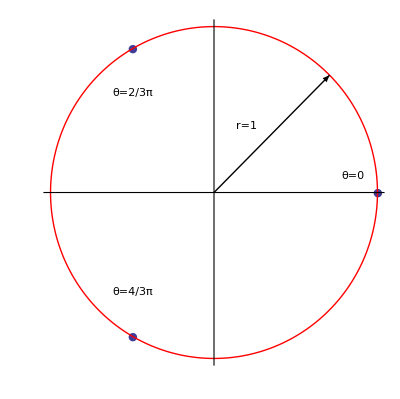

Mondiale.eps

```mathematica
Show[ListPolarPlot[{{0,1},{2/3π,1},{4/3π,1}},PlotMarkers->{Automatic,Medium}],ParametricPlot[{Cos[θ],Sin[θ]},{θ,0,2π},PlotStyle->Directive[Red,Thick]],Graphics[Text[Style["θ=0",Large],{0.85,0.1}]],Graphics[Text[Style["θ=2/3π",Large],{-0.5,0.6}]],Graphics[Text[Style["θ=4/3π",Large],{-0.5,-0.6}]],Graphics[{Thick,Arrow[{{0,0},{1/Sqrt[2],1/Sqrt[2]}}]}],Graphics[Text[Style["r=1",Large],{0.2,0.4}]],Ticks->None]

Export["Mondiale.eps",%,"EPS"]
```